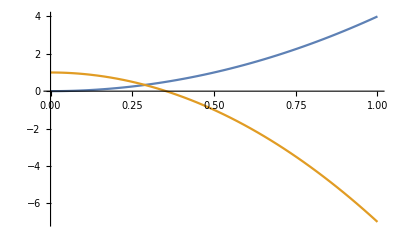

```mathematica
Plot[{4t^2,1-8t^2},{t,0,1}]
```

## Random walker

```mathematica
A=Import["~/Programs/MonteCarlo_for_JammedStates/Data/Sz_dt0.1.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<3&)];
A=Cases[A,_?(#[[2]]≠1&)](*if σ doesn't change -> dont print it*);
A=A[[;;,{1,3,2}]](*x,t,σ*);
ListDensityPlot[A]
```

-Graphics-

## Some results on exponent

-Graphics-

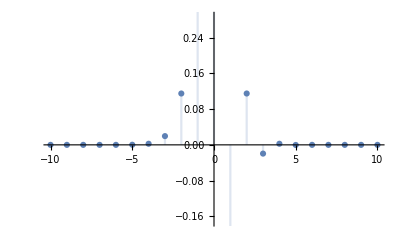

```mathematica
DiscretePlot[{BesselJ[n,-1],{n,-10,10}]
```

```mathematica
BesselJ[-2,x]//Simplify
```

BesselJ[2,x]